```mathematica
VarMix =ParallelTable[
Var=
{ Table[
n=10;
mu = RandomVariate[NormalDistribution[-15,0.5],n];
sig = Table[x,{n}];(1/n^2)*(Sum[n*sig[[i]]^2 + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,1000}],
 Table[
n=10;
mu = RandomVariate[NormalDistribution[-15,1],n];
sig = Table[x,{n}];(1/n^2)*(Sum[n*sig[[i]]^2 + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,1000}]},
(*{x,Mean[Var]},*)
{x,0.1,2,0.1}];
```

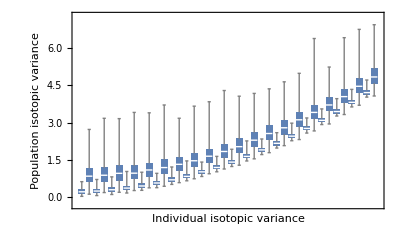

```mathematica
IndPopVarPlot=BoxWhiskerChart[VarMix,ChartStyle->ColorData[97,1],(*ChartLabels->Table[If[Mod[x+1,IntegerPart[x]+1]==0,IntegerPart[x],""],{x,0.1,2,0.05}],*)
FrameLabel->{"Individual isotopic variance","Population isotopic variance"}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf",IndPopVarPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf

```mathematica
VarMix1 =ParallelTable[
Var=
 Table[
n=50;
mu = RandomVariate[NormalDistribution[-15,0.5],n];
sig = Table[x,{n}];(1/n^2)*(Sum[n*sig[[i]]^2 + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,1000}],
(*{x,Mean[Var]},*)
{x,0.1,2,0.05}];
VarMix2 =ParallelTable[
Var=Table[
n=50;
mu = RandomVariate[NormalDistribution[-15,5],n];
sig = Table[x,{n}];(1/n^2)*(Sum[n*sig[[i]]^2 + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,1000}],
(*{x,Mean[Var]},*)
{x,0.1,2,0.05}];
```

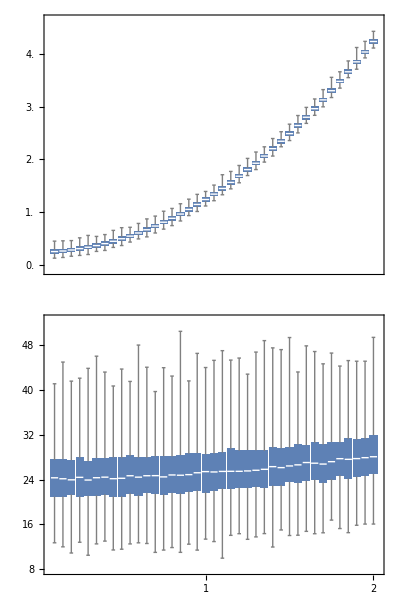
-Graphics-Population isotopic varianceIndividual isotopic variance

```mathematica
IndPopVarPlot2=
Labeled[Column[{
BoxWhiskerChart[VarMix1,ChartStyle->ColorData[97,1],(*ChartLabels->Table[If[Mod[x+1,IntegerPart[x]+1]==0,IntegerPart[x],""],{x,0.1,2,0.05}],*)
ImageSize->300,FrameTicks->{Automatic,Table[x,{x,0,5,0.5}],None,None}],
IndPopVarPlot=BoxWhiskerChart[VarMix2,ChartStyle->ColorData[97,1],ChartLabels->Table[If[Mod[x+1,IntegerPart[x]+1]==0,IntegerPart[x],""],{x,0.1,2,0.05}],
ImageSize->300]
},Spacings->-0.25],
TraditionalForm/@{Rotate["Population isotopic variance",90Degree],"Individual isotopic variance"},{Left,Bottom},Spacings->{1,0},LabelStyle->"Panel"]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar2.pdf",IndPopVarPlot2]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar2.pdf

```mathematica
Length[VarMix]
```

25

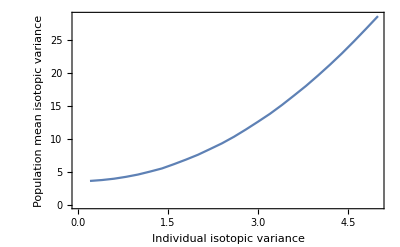

```mathematica
ListPlot[VarMix,Frame->True,FrameLabel->{"Individual isotopic variance","Population mean isotopic variance"},Joined->True]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf",IndPopVarPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf

```mathematica
Table[If[IntegerQ[x],ToString[x]," "],{x,1,10,0.5}]
```

{ , , , , , , , , , , , , , , , , , , }

```mathematica
ToInt[x_] :=If[IntegerQ[x],ToString[x],""]
```

```mathematica
Table[x,{x,1,10,0.5}]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

```mathematica
ToInt/@Table[x,{x,1,10,0.5}]
```

{,,,,,,,,,,,,,,,,,,}

```mathematica
IntegerQ[1.0]
```

False

```mathematica
Mod[1.5,IntegerPart[1.5]]
```

0.5